## Authors Informations

#### Authors: Huan Souza.b9* and A. C. Lehum.b9** Date: April 09, 2021 Filiation: Federal University of Pará.b9 Email: huan.souza@icen.ufpa.br*, lehum@ufpa.br**

# Quantum electrodynamics coupled to linearized gravity

To compute the diagrams, we have used FeynCalc [1], FeynArts [2], FeynHelpers [3] and TARCER [4].

```mathematica
description="Scalar electrodynamics coupled to linearized gravity";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts","TARCER","FeynHelpers"};
Get["FeynCalc`"]
$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

TARCER 2.0, for more information see the accompanying publication. If you use TARCER in your research, please cite

• R. Mertig and R. Scharf, Comput. Phys. Commun., 111, 265-273, 1998, arXiv:hep-ph/9801383

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
(*We keep the scaleless B0 functions*)
$KeepLogDivergentScalelessIntegrals=True;
```

```mathematica
(*These are some definitions to make our outputs look better*)
MakeBoxes[mu,TraditionalForm]:="μ";
MakeBoxes[nu,TraditionalForm]:="ν";
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[p4,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
MakeBoxes[m1,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(1\)]\)";
```

```mathematica
(*Also, we make this defition because it is the definition used by TARCER*)
ScalarProduct[p,p]=p^2;
```

## Scalar-QED

## 1-loop counterterms

First, let us see if linearized gravity can change the behaviour of the electric charge β-function in one-loop order.

```mathematica
(*We are using a model that we created and the directory with it should be inside the directory $UserBaseDirectory/Applications/FeynCalc/FeynArts/Models*)
```

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_Scalar_QED","Einstein_Scalar_QED"}],Model->FileNameJoin[{"Einstein_Scalar_QED","Einstein_Scalar_QED"}]};
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4}];
topCT1[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4}];
seph1=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields1]&)[top1[1,1]];
sephCT1=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields1]&)[topCT1[1,1]];
```

```mathematica
(*Here, we put together the diagrams with and without counterterms*)
diag1=seph1[[0]][Sequence@@seph1,Sequence@@sephCT1];
```

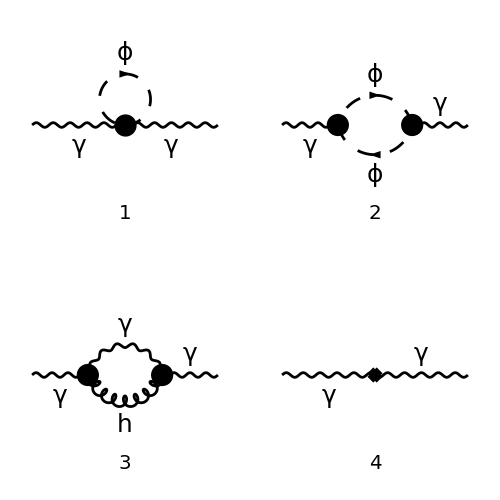

```mathematica
Paint[diag1,ColumnsXRows->{2,2},SheetHeader->{"Photon self-energy"},Numbering->Simple,ImageSize->{500,500}];
```

### γ wave function counterterm

```mathematica
(*To create the amplitude, we use CreateFeynAmp and choose to cut the external legs. Then, to convert the output to the FeynCalc form, we use FCFAConvert and choose the incoming momentum and the outgoing momentum to be p, the loop momentum to be k. Besides that, the option List->False sums the contributions of each diagram instead of make a list of them. The option SMP->True uses the standard model parameters. Also, we do this computation in D dimensions and the indices of the polarization tensor are μ and ν.*)
ampse1[0]=FCFAConvert[CreateFeynAmp[diag1,Truncated->True],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu},Contract->True,FinalSubstitutions->{Z3->1+SMP["d_A"]}]
```

-(ⅈ κ^2 D^2 g^μν (k·p)^2)/(128 π^4 k^2.(k-p)^2)+(7 ⅈ κ^2 D g^μν (k·p)^2)/(64 π^4 k^2.(k-p)^2)-(ⅈ κ^2 g^μν (k·p)^2)/(4 π^4 k^2.(k-p)^2)-(ⅈ κ^2 D^2 g^μν p^4)/(128 π^4 k^2.(k-p)^2)+(7 ⅈ κ^2 D g^μν p^4)/(64 π^4 k^2.(k-p)^2)-(3 ⅈ κ^2 g^μν p^4)/(16 π^4 k^2.(k-p)^2)-(ⅈ κ^2 p^μ p^ν k^2)/(16 π^4 k^2.(k-p)^2)+(ⅈ κ^2 D^2 p^μ k^ν (k·p))/(128 π^4 k^2.(k-p)^2)-(7 ⅈ κ^2 D p^μ k^ν (k·p))/(64 π^4 k^2.(k-p)^2)+(ⅈ κ^2 p^μ k^ν (k·p))/(4 π^4 k^2.(k-p)^2)+(ⅈ κ^2 D^2 k^μ p^ν (k·p))/(128 π^4 k^2.(k-p)^2)-(7 ⅈ κ^2 D k^μ p^ν (k·p))/(64 π^4 k^2.(k-p)^2)+(ⅈ κ^2 k^μ p^ν (k·p))/(4 π^4 k^2.(k-p)^2)-(ⅈ κ^2 D^2 p^μ p^ν (k·p))/(64 π^4 k^2.(k-p)^2)+(7 ⅈ κ^2 D p^μ p^ν (k·p))/(32 π^4 k^2.(k-p)^2)-(3 ⅈ κ^2 p^μ p^ν (k·p))/(8 π^4 k^2.(k-p)^2)-(ⅈ κ^2 D^2 k^μ k^ν p^2)/(128 π^4 k^2.(k-p)^2)+(7 ⅈ κ^2 D k^μ k^ν p^2)/(64 π^4 k^2.(k-p)^2)-(ⅈ κ^2 k^μ k^ν p^2)/(4 π^4 k^2.(k-p)^2)+(ⅈ κ^2 D^2 p^μ p^ν p^2)/(128 π^4 k^2.(k-p)^2)-(7 ⅈ κ^2 D p^μ p^ν p^2)/(64 π^4 k^2.(k-p)^2)+(3 ⅈ κ^2 p^μ p^ν p^2)/(16 π^4 k^2.(k-p)^2)+(ⅈ κ^2 g^μν k^2 p^2)/(16 π^4 k^2.(k-p)^2)+(ⅈ κ^2 D^2 g^μν (k·p) p^2)/(64 π^4 k^2.(k-p)^2)-(7 ⅈ κ^2 D g^μν (k·p) p^2)/(32 π^4 k^2.(k-p)^2)+(3 ⅈ κ^2 g^μν (k·p) p^2)/(8 π^4 k^2.(k-p)^2)+(ⅈ g^μν e^2)/(8 π^4 (k^2-m^2))-(ⅈ k^μ k^ν e^2)/(16 π^4 (k^2-m^2).((k-p)^2-m^2))-(ⅈ (k-p)^μ k^ν e^2)/(16 π^4 (k^2-m^2).((k-p)^2-m^2))+(ⅈ k^μ (p-k)^ν e^2)/(16 π^4 (k^2-m^2).((k-p)^2-m^2))+(ⅈ (k-p)^μ (p-k)^ν e^2)/(16 π^4 (k^2-m^2).((k-p)^2-m^2))+p^μ p^ν δ_A-g^μν p^2 δ_A

```mathematica
(*Now, we use TID to convert the amplitude to the Passarino-Veltman integrals form.*)
ampse1[1]=TID[ampse1[0],k,ToPaVe->True]
```

-((D^2-14 D+32) κ^2 p^2 B_0(p^2,0,0) (-(1-D) p^2 g^μν+2 (1-D) p^μ p^ν+D p^μ p^ν-p^2 g^μν))/(512 π^2 (1-D))+(e^2 B_0(p^2,m^2,m^2) (-(1-D) p^2 p^μ p^ν-D p^2 p^μ p^ν-4 m^2 p^2 g^μν+p^4 g^μν+4 m^2 p^μ p^ν))/(16 π^2 (1-D) p^2)+(e^2 A_0(m^2) (-(1-D) p^2 g^μν-D p^μ p^ν-p^2 g^μν+2 p^μ p^ν))/(8 π^2 (1-D) p^2)+δ_A (p^μ p^ν-p^2 g^μν)

```mathematica
(*To evaluate this result, we are using the function from FeynHelpers, PaXEvaluate*)
ampse1[2]=PaXEvaluate[ampse1[1]]
```

-(log(-μ^2/p^2) g^μν p^4 κ^2)/(96 π^2)+((-1+6 ℽ+6 log(π)) g^μν p^4 κ^2)/(576 π^2)-(g^μν p^4 κ^2)/(96 ε π^2)+(log(-μ^2/p^2) p^μ p^ν p^2 κ^2)/(96 π^2)-((-1+6 ℽ+6 log(π)) p^μ p^ν p^2 κ^2)/(576 π^2)+(p^μ p^ν p^2 κ^2)/(96 ε π^2)+(m^2 g^μν e^2)/(6 π^2)+(p^μ p^ν e^2)/(48 ε π^2)-(g^μν p^2 e^2)/(48 ε π^2)-(log((2 m^2-p^2+√(p^2 (p^2-4 m^2)))/(2 m^2)) g^μν √(p^2 (p^2-4 m^2)) e^2)/(48 π^2)+(m^2 log((2 m^2-p^2+√(p^2 (p^2-4 m^2)))/(2 m^2)) g^μν √(p^2 (p^2-4 m^2)) e^2)/(12 π^2 p^2)+(log((2 m^2-p^2+√(p^2 (p^2-4 m^2)))/(2 m^2)) p^μ p^ν √(p^2 (p^2-4 m^2)) e^2)/(48 π^2 p^2)-(m^2 log((2 m^2-p^2+√(p^2 (p^2-4 m^2)))/(2 m^2)) p^μ p^ν √(p^2 (p^2-4 m^2)) e^2)/(12 π^2 p^4)-(m^2 p^μ p^ν e^2)/(6 π^2 p^2)+(p^μ p^ν (3 log(μ^2/m^2) e^2-3 log(π) e^2-3 ℽ e^2+8 e^2+144 π^2 δ_A))/(144 π^2)-(g^μν p^2 (3 log(μ^2/m^2) e^2-3 log(π) e^2-3 ℽ e^2+8 e^2+144 π^2 δ_A))/(144 π^2)

```mathematica
(*In order to compute the counterterm, we only need the divegent part of it*)
ampse1[3]=SelectNotFree2[ampse1[2],{Epsilon,SMP["d_A"]}]//Factor
```

((p^μ p^ν-p^2 g^μν) (96 π^2 ε δ_A+2 e^2+κ^2 p^2))/(96 π^2 ε)

```mathematica
(*Once all terms are multiplied by Pair[LorentzIndex[mu,D],Momentum[p,D]]*Pair[LorentzIndex[nu,D],Momentum[p,D]]-Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]*Pair[Momentum[p,D],Momentum[p,D]], to compute the counterterms, we only need Π(p).*)
ampse1[4]=Coefficient[ampse1[3],(Pair[LorentzIndex[mu,D],Momentum[p,D]]*Pair[LorentzIndex[nu,D],Momentum[p,D]]-Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]*Pair[Momentum[p,D],Momentum[p,D]])]//Simplify
```

(96 π^2 ε δ_A+2 e^2+κ^2 p^2)/(96 π^2 ε)

```mathematica
(*Finally, we find the countertem*)
Solve[SelectFree2[ampse1[4],p]==0,SMP["d_A"]]
```

{{δ_A→-e^2/(48 π^2 ε)}}

We can notice that there is no contribution of order κ.b2. Then, linearized gravity does not contribute to the electrical charge β-function in one-loop order.

## γ self energy 2-loops

Now we are going to compute the 2-loops photon self-energy diagrams. In order to do so, we have used TARCER.

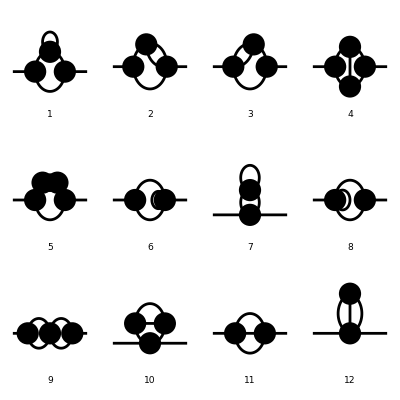

```mathematica
(*The topologies of the two-loops self-energy diagrams are the following. Notice that we have introduced diagram with 5 adjacencies because of interactions with five fields in one point, such as hϕ⁴.*)
top2l=CreateTopologies[2,1->1,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
Paint[top2l,ColumnsXRows->{4,3},SheetHeader->{"Self-energy two-loop topologies"},Numbering->Simple,ImageSize->{400,400}];
```

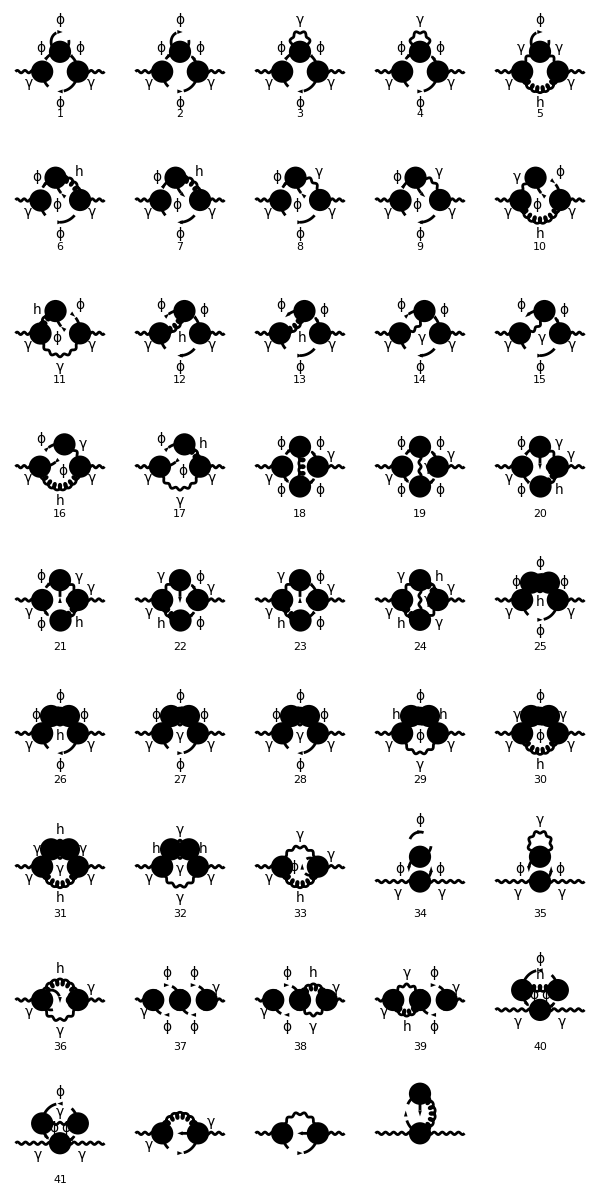

```mathematica
(*Now we insert the fields of our model*)
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_Scalar_QED","Einstein_Scalar_QED"}],Model->FileNameJoin[{"Einstein_Scalar_QED","Einstein_Scalar_QED"}]};
top2[i_,j_]:=CreateTopologies[2,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
seph2a=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields1]&)[top2[1,1]];
Paint[seph2a,ColumnsXRows->{5,9},SheetHeader->{"2-loops photon self-energy"},Numbering->Simple,ImageSize->{600,1200}];
```

As we can see from the figure above, there are diagrams with two gravitons, which would contribute with terms of order κ⁴, but we restrict ourselves to order κ.b2. Then, we delete those diagrams.

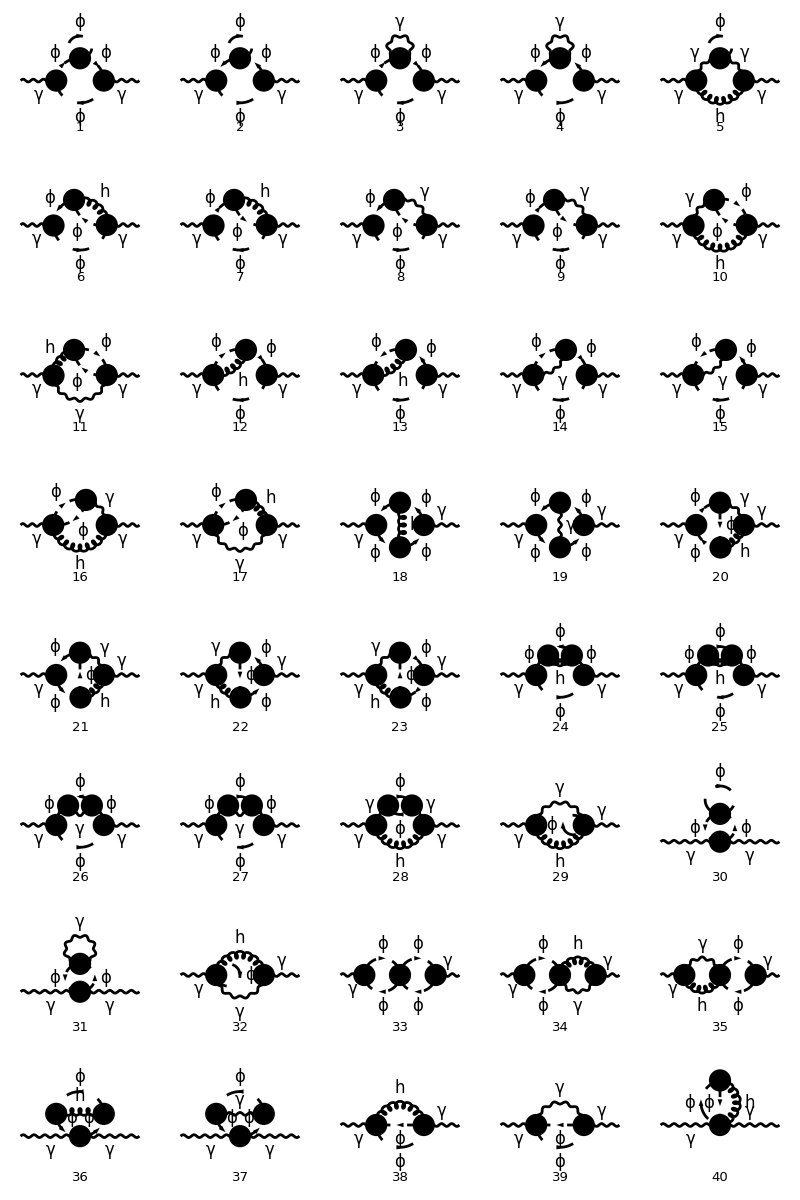

```mathematica
seph2=DiagramDelete[seph2a,{24,29,31,32}];
Paint[seph2,ColumnsXRows->{5,8},SheetHeader->{"2-loops photon self-energy"},Numbering->Simple,ImageSize->{800,1200}];
```

### Helper functions

In this section, we create some helper functions to compute the diagrams.

```mathematica
(*The first helper function is createAmplitudes. It creates the amplitudes of a diagram from a process(such as the photon self-energy).*)
createAmplitudes[allprocesses_,diagram_]:=(Expand[Simplify[FCFAConvert[#1,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k1,k2},List->False,SMP->True,LorentzIndexNames->{mu,nu},Contract->True,ChangeDimension->D]]]&)[CreateFeynAmp[DiagramExtract[allprocesses,diagram],Truncated->True]]

(*Now, because TARCER can only deal with scalar integrals, we need to find a way to transform our tensorial integrals in scalar ones. To do so, we notice that our integrals can be rewritten as Π^μν=p^2*g^μν*A + p^μ*p^ν*B, where A and B are scalar integrals. Then, we find that A=1/((D-1)*p^2)*(g^μν-p^μ*p^ν/p^2)*Π^μν and 
B=-1/((D-1)*p^2)*(g^μν-D*p^μ*p^ν/p^2)*Π^μν. Then, we define the functions findA and findB to find what are A and B for each amplitude.*) 
findA[amplitude_]:=(Expand[Simplify[DotExpand[#1]]]&)[(Contract[#1]&)[1/((D-1)*Pair[Momentum[p,D],Momentum[p,D]])*(Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]-Pair[LorentzIndex[mu,D],Momentum[p,D]]*Pair[LorentzIndex[nu,D],Momentum[p,D]]/Pair[Momentum[p,D],Momentum[p,D]])*amplitude]]
findB[amplitude_]:=(Expand[Simplify[DotExpand[#1]]]&)[(Contract[#1]&)[-1/((D-1)*Pair[Momentum[p,D],Momentum[p,D]])*(Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]-D*Pair[LorentzIndex[mu,D],Momentum[p,D]]*Pair[LorentzIndex[nu,D],Momentum[p,D]]/Pair[Momentum[p,D],Momentum[p,D]])*amplitude]]

(*Now, it is important to notice that TARCER can only compute scalar integrals and cannot compute amplitudes. Because of that, we must isolate the integrals and solve one by one. To do so, we first isolate the integrals in the amplitude using the function FCLoopIsolate and make a list in which each element is the part of the amplitude proportional to one specific integral, to do so we use List @@.*)
isolateIntegralsAndMakeList[scalarAmplitude_]:=Expand[List@@FCLoopIsolate[scalarAmplitude,{k1,k2},Head->loopInt]]

(*Once we have the list of integrals, we can compute them. To do this, we define the function integralsCompute. The first thing we have to do is to pick one element of the list of integrals. To do so, we use the function Table. This function enables us to use an index i that goes from first one up to a desired number, in our case, this number is the length of our list of integrals. Then, we select the element of number i in our list with listOfIntegrals[[i]]. After that, we take only the integral and then set loopInt->Identity to be able to compute it. Next we convert the integrals to TARCER notation using ToTFI and use TarcerRecurse to simplify the integrals. Then, we need to coupled our simplified integral once again with the prefactors that we have discarded. Finally, after compute all the integrals, we use Plus@@ to sum all the elements in the list.*)
integralsCompute[listOfIntegrals_]:=Plus@@Table[(Expand[Simplify[#1]]&)[(listOfIntegrals[[i]]/.{Cases2[listOfIntegrals[[i]],loopInt][[1]]->#1}&)[(Expand[TarcerRecurse[#1]]&)[(ToTFI[#1,k1,k2,p]&)[(#1/.{loopInt->Identity}&)[(Cases2[#1,loopInt][[1]]&)[listOfIntegrals[[i]]]]]]]],{i,Length[listOfIntegrals]}]

(*At last, we substitute the results we have found for A and B in our expression for the tensorial amplitude.*)
findFinalResult[computedA_,computedB_]:=Expand[MTD[mu,nu]*SPD[p,p]*computedA+Pair[LorentzIndex[mu,D],Momentum[p,D]]*Pair[LorentzIndex[nu,D],Momentum[p,D]]*computedB]
```

### Computation

In this section, we do the computation of all diagrams. As you my notice, we summed amplitudes 30, 31 and 39 with α*amplitude 1. We did this because amplitudes 30, 31 and 39 have only one term. Then, when we use List@@ in function isolateIntegralsAndMakeList, we won’t end up with a list of one element. Instead, Mathematica will make a list with all elements that are multiplied. To illustrate this, see the example below:

```mathematica
List@@(a*b)
```

{a,b}

As we can see, instead of have a list with only the element ab, we have a list with two elements, a and b. In our case, this will be a problem when we deal amplitudes with only one element, because it will split it in several parts and in the end, when we use Plus@@, we will have the wrong result in hands. See the example below,

```mathematica
List@@(MTD[mu,nu]*SMP["e"]*FAD[k,k-p])
Plus@@%
```

{1/(k^2.(k-p)^2),g^μν,e}

1/(k^2.(k-p)^2)+e+g^μν

We end up with a completely wrong result.

```mathematica
AbsoluteTiming[For[
i=1,i≤29,i++,{
amp[i]=createAmplitudes[seph2,{i}],
A[i]=findA[amp[i]],
B[i]=findB[amp[i]],
listA[i]=isolateIntegralsAndMakeList[A[i]],
listB[i]=isolateIntegralsAndMakeList[B[i]],
computedA[i]=integralsCompute[listA[i]],
computedB[i]=integralsCompute[listB[i]],
final[i]=findFinalResult[computedA[i],computedB[i]]//Expand//Simplify//Expand}
];
amp[30]=createAmplitudes[seph2,{30}]+α*createAmplitudes[seph2,{1}];
A[30]=findA[amp[30]];
B[30]=findB[amp[30]];
listA[30]=isolateIntegralsAndMakeList[A[30]];
listB[30]=isolateIntegralsAndMakeList[B[30]];
computedA[30]=integralsCompute[listA[30]];
computedB[30]=integralsCompute[listB[30]];
final[30]=Limit[findFinalResult[computedA[30],computedB[30]],α->0]//Expand//Simplify//Expand;
amp[31]=createAmplitudes[seph2,{31}]+α*createAmplitudes[seph2,{1}];
A[31]=findA[amp[31]];
B[31]=findB[amp[31]];
listA[31]=isolateIntegralsAndMakeList[A[31]];
listB[31]=isolateIntegralsAndMakeList[B[31]];
computedA[31]=integralsCompute[listA[31]];
computedB[31]=integralsCompute[listB[31]];
final[31]=Limit[findFinalResult[computedA[31],computedB[31]],α->0]//Expand//Simplify//Expand;
For[
i=32,i≤38,i++,{
amp[i]=createAmplitudes[seph2,{i}],
A[i]=findA[amp[i]],
B[i]=findB[amp[i]],
listA[i]=isolateIntegralsAndMakeList[A[i]],
listB[i]=isolateIntegralsAndMakeList[B[i]],
computedA[i]=integralsCompute[listA[i]],
computedB[i]=integralsCompute[listB[i]],
final[i]=findFinalResult[computedA[i],computedB[i]]//Expand//Simplify//Expand}
];
amp[39]=createAmplitudes[seph2,{39}]+α*createAmplitudes[seph2,{1}];
A[39]=findA[amp[39]];
B[39]=findB[amp[39]];
listA[39]=isolateIntegralsAndMakeList[A[39]];
listB[39]=isolateIntegralsAndMakeList[B[39]];
computedA[39]=integralsCompute[listA[39]];
computedB[39]=integralsCompute[listB[39]];
final[39]=Limit[findFinalResult[computedA[39],computedB[39]],α->0]//Expand//Simplify//Expand;
amp[40]=createAmplitudes[seph2,{40}];
A[40]=findA[amp[40]];
B[40]=findB[amp[40]];
listA[40]=isolateIntegralsAndMakeList[A[40]];
listB[40]=isolateIntegralsAndMakeList[B[40]];
computedA[40]=integralsCompute[listA[40]];
computedB[40]=integralsCompute[listB[40]];
final[40]=findFinalResult[computedA[40],computedB[40]]//Expand//Simplify//Expand;]
```

{670.99,Null}

```mathematica
(*Because the result must be gauge invariant, we expect that A+B=0*)
totalA=Limit[Sum[computedA[i],{i,1,40}],α->0];
totalB=Limit[Sum[computedB[i],{i,1,40}],α->0];
totalA+totalB//Simplify//Expand
```

0

```mathematica
(*The result is gauge invariant*)
```

```mathematica
totalSum=Sum[final[i],{i,1,40}]//Expand//Simplify//Expand;
Pimunu2l=Factor[totalSum]
```

((p^2 g^μν-p^μ p^ν) e^2 (20 κ^2 m^2 (A_{1,m}^(D))^2 D^8+κ^2 p^2 (A_{1,m}^(D))^2 D^8+κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^8-48 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^8-6 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^8-492 κ^2 m^2 (A_{1,m}^(D))^2 D^7-28 κ^2 p^2 (A_{1,m}^(D))^2 D^7-28 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^7-48 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^7-24 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^7+1896 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^7+150 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^7+64 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^7-2 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^7-8 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^7+5112 κ^2 m^2 (A_{1,m}^(D))^2 D^6+323 κ^2 p^2 (A_{1,m}^(D))^2 D^6+192 e^2 (A_{1,m}^(D))^2 D^6-384 λ (A_{1,m}^(D))^2 D^6+323 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^6+960 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^6+264 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^6+12 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^6+96 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^6-96 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^6-26296 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^6-1558 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^6-2272 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^6+52 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^6+360 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^6-28904 κ^2 m^2 (A_{1,m}^(D))^2 D^5-2008 κ^2 p^2 (A_{1,m}^(D))^2 D^5-2112 e^2 (A_{1,m}^(D))^2 D^5+4992 λ (A_{1,m}^(D))^2 D^5+48 κ^2 m^6 (B_({1,m}{1,m})^(D))^2 D^5+3 κ^2 m^2 p^4 (B_({1,m}{1,m})^(D))^2 D^5-24 κ^2 m^4 p^2 (B_({1,m}{1,m})^(D))^2 D^5-2008 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^5-7824 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^5-696 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^5+768 λ m^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^5-300 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^5-384 m^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^5+96 κ^2 m^2 p^4 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^5-192 κ^2 m^4 p^2 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^5-1536 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^5-384 κ^2 m^6 p^2 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^5+1536 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^5+768 κ^2 m^6 p^2 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^5+184184 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^5+8706 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^5-768 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^5+27456 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^5-542 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^5-4696 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^5+96560 κ^2 m^2 (A_{1,m}^(D))^2 D^4+7376 κ^2 p^2 (A_{1,m}^(D))^2 D^4+9408 e^2 (A_{1,m}^(D))^2 D^4-25728 λ (A_{1,m}^(D))^2 D^4-720 κ^2 m^6 (B_({1,m}{1,m})^(D))^2 D^4-45 κ^2 m^2 p^4 (B_({1,m}{1,m})^(D))^2 D^4+360 κ^2 m^4 p^2 (B_({1,m}{1,m})^(D))^2 D^4+7376 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^4+33792 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^4-2616 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^4-8448 λ m^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^4+2904 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^4+4992 m^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^4-384 p^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^4-1344 κ^2 m^2 p^4 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^4+2304 κ^2 m^4 p^2 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^4+9504 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^4+4608 κ^2 m^6 p^2 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^4-9888 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^4-9216 κ^2 m^6 p^2 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^4-737816 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^4-28436 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^4+9216 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^4-160800 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^4+2932 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^4+28664 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^4-194752 κ^2 m^2 (A_{1,m}^(D))^2 D^3-16336 κ^2 p^2 (A_{1,m}^(D))^2 D^3-22080 e^2 (A_{1,m}^(D))^2 D^3+67200 λ (A_{1,m}^(D))^2 D^3+4416 κ^2 m^6 (B_({1,m}{1,m})^(D))^2 D^3+360 κ^2 m^2 p^4 (B_({1,m}{1,m})^(D))^2 D^3-2496 κ^2 m^4 p^2 (B_({1,m}{1,m})^(D))^2 D^3-1536 m^4 e^2 (B_({1,m}{1,m})^(D))^2 D^3+768 m^2 p^2 e^2 (B_({1,m}{1,m})^(D))^2 D^3-16432 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^3-83712 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^3+19776 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^3-96 κ^2 p^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^3+34560 λ m^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^3-13056 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^3-23424 m^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^3+2688 p^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^3+7200 κ^2 m^2 p^4 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^3-10560 κ^2 m^4 p^2 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^3-28800 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^3-21120 κ^2 m^6 p^2 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^3+32640 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^3+42240 κ^2 m^6 p^2 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^3+1758944 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^3+54856 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^3-42240 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^3+509440 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^3-8888 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^3-94208 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^3-3072 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^3+768 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D^3+231296 κ^2 m^2 (A_{1,m}^(D))^2 D^2+21232 κ^2 p^2 (A_{1,m}^(D))^2 D^2+29184 e^2 (A_{1,m}^(D))^2 D^2-93696 λ (A_{1,m}^(D))^2 D^2-13248 κ^2 m^6 (B_({1,m}{1,m})^(D))^2 D^2-1332 κ^2 m^2 p^4 (B_({1,m}{1,m})^(D))^2 D^2+8352 κ^2 m^4 p^2 (B_({1,m}{1,m})^(D))^2 D^2+9216 m^4 e^2 (B_({1,m}{1,m})^(D))^2 D^2-4608 m^2 p^2 e^2 (B_({1,m}{1,m})^(D))^2 D^2+21712 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^2+119040 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^2-47520 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^2+480 κ^2 p^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^2-65280 λ m^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^2+29280 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^2+51840 m^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^2-6912 p^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^2-18240 κ^2 m^2 p^4 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^2+23040 κ^2 m^4 p^2 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^2+44544 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^2+46080 κ^2 m^6 p^2 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^2-57984 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^2-92160 κ^2 m^6 p^2 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^2-2456320 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^2-59568 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^2+92160 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^2-886272 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^2+15280 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^2+170816 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^2+15360 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^2-3840 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D^2-147456 κ^2 m^2 (A_{1,m}^(D))^2 D-14784 κ^2 p^2 (A_{1,m}^(D))^2 D-20736 e^2 (A_{1,m}^(D))^2 D+66048 λ (A_{1,m}^(D))^2 D+19008 κ^2 m^6 (B_({1,m}{1,m})^(D))^2 D+2112 κ^2 m^2 p^4 (B_({1,m}{1,m})^(D))^2 D-12672 κ^2 m^4 p^2 (B_({1,m}{1,m})^(D))^2 D-16896 m^4 e^2 (B_({1,m}{1,m})^(D))^2 D+8448 m^2 p^2 e^2 (B_({1,m}{1,m})^(D))^2 D-15552 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D-89856 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D+52224 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D-768 κ^2 p^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D+56832 λ m^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D-31680 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D-54528 m^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D+7680 p^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D+21504 κ^2 m^2 p^4 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D-23808 κ^2 m^4 p^2 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D-33024 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D-47616 κ^2 m^6 p^2 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D+52224 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D+95232 κ^2 m^6 p^2 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D+1842240 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D+32000 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D-95232 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D+789632 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D-13824 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D-159296 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D-24576 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D+6144 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D+38400 κ^2 m^2 (A_{1,m}^(D))^2+4224 κ^2 p^2 (A_{1,m}^(D))^2+6144 e^2 (A_{1,m}^(D))^2-18432 λ (A_{1,m}^(D))^2-10368 κ^2 m^6 (B_({1,m}{1,m})^(D))^2-1152 κ^2 m^2 p^4 (B_({1,m}{1,m})^(D))^2+6912 κ^2 m^4 p^2 (B_({1,m}{1,m})^(D))^2+9216 m^4 e^2 (B_({1,m}{1,m})^(D))^2-4608 m^2 p^2 e^2 (B_({1,m}{1,m})^(D))^2+4608 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D)+27648 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D)-22272 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D)+384 κ^2 p^4 A_{1,m}^(D) B_({1,m}{1,m})^(D)-18432 λ m^2 A_{1,m}^(D) B_({1,m}{1,m})^(D)+13056 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D)+21504 m^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D)-3072 p^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D)-9216 κ^2 m^2 p^4 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D)+9216 κ^2 m^4 p^2 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D)+9216 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D)+18432 κ^2 m^6 p^2 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D)-18432 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D)-36864 κ^2 m^6 p^2 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D)-566784 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D)-6144 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D)+36864 m^2 e^2 J_({1,m}{1,m}{1,0})^(D)-277248 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D)+4992 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D)+58368 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D)+12288 m^4 e^2 J_({2,m}{1,m}{1,0})^(D)-3072 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D)))/(49152 (D-4) (D-3) (D-2) (D-1)^2 m^2 p^2 π^8)

All of this integrals are know and they can be found at [5, 6].

## Fermionic-QED

## γ self energy 2-loops

In the fermionic case, we will follow the same procedure that we did before in the scalar case.

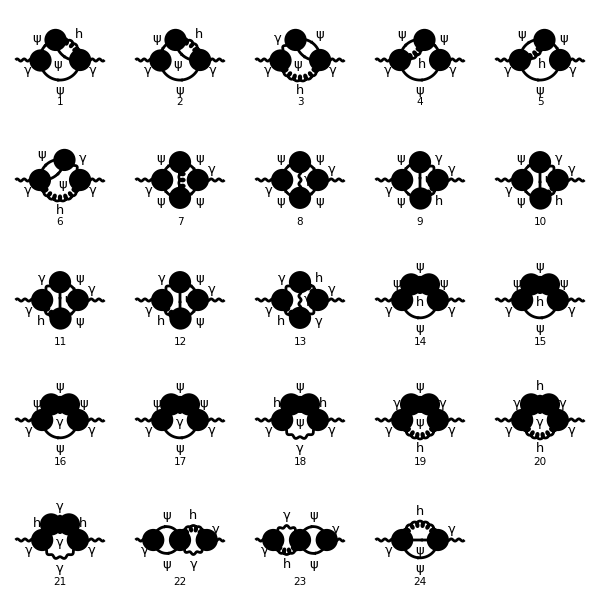

```mathematica
fields2={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_QED","Einstein_QED"}],Model->FileNameJoin[{"Einstein_QED","Einstein_QED"}]};
top2[i_,j_]:=CreateTopologies[2,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
sephF2=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields2]&)[top2[1,1]];
Paint[sephF2,ColumnsXRows->{5,5},SheetHeader->{"Photon self-energy"},Numbering->Simple,ImageSize->{600,600}];
```

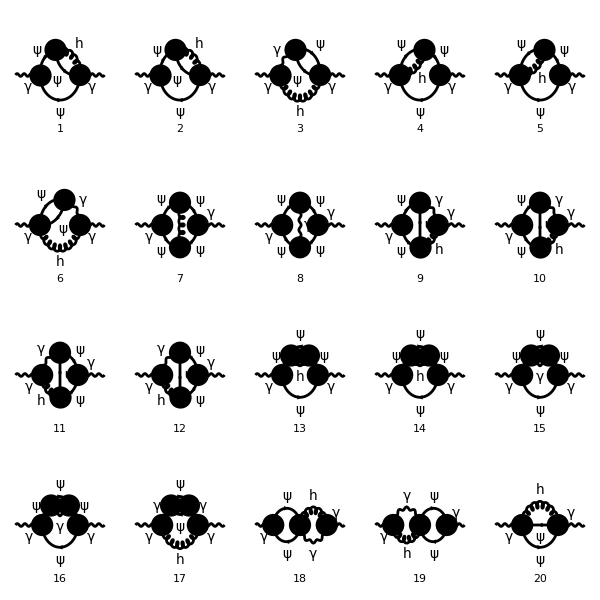

```mathematica
sephF2a=DiagramDelete[seph2,{13,18,20,21}];
Paint[seph2a,ColumnsXRows->{5,4},SheetHeader->{"Photon self-energy"},Numbering->Simple,ImageSize->{600,600}];
```

### Computation

Now, we are going to use the same helper functions we defined before. We just need to use one additional function, which is DiracSimplify, once we are dealing with fermions.

```mathematica
AbsoluteTiming[For[
i=1,i≤20,i++,{
amp[i]=createAmplitudes[sephF2a,{i}],
ampD[i]=DiracSimplify[amp[i]],
A[i]=findA[ampD[i]],
B[i]=findB[ampD[i]],
listA[i]=isolateIntegralsAndMakeList[A[i]],
listB[i]=isolateIntegralsAndMakeList[B[i]],
computedA[i]=integralsCompute[listA[i]],
computedB[i]=integralsCompute[listB[i]],
final[i]=findFinalResult[computedA[i],computedB[i]]//Expand//Simplify//Expand}
];]
```

{1023.15,Null}

```mathematica
totalA=Sum[computedA[i],{i,1,20}];
totalB=Sum[computedB[i],{i,1,20}];
totalA+totalB//Simplify//Expand
```

0

```mathematica
(*The result is gauge invariant*)
```

```mathematica
totalSum=Sum[final[i],{i,1,20}]/.{Beta-> EulerGamma}//Expand//Simplify//Expand;
Pimunu2l=Factor[totalSum]//Simplify
```

((p^2 g^μν-p^μ p^ν) e^2 ((48 κ^2 (D^4-10 D^3+35 D^2-50 D+24) (4 m^2-p^2) (4 (D-2) m^2+(D^2-4 D+2) p^2) B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) p^2-3 (D^2-5 D+6) (κ^2 (64 (D^2-2 D+4) m^6+16 (D^4-12 D^3+32 D^2-14 D-16) p^2 m^4-4 (4 D^4-38 D^3+125 D^2-132 D+32) p^4 m^2+(3 D^4-22 D^3+72 D^2-88 D+32) p^6)-64 (D-1) (32 m^4+4 (D^3-11 D^2+38 D-40) p^2 m^2-(D^3-9 D^2+30 D-32) p^4) e^2) (B_({1,m}{1,m})^(D))^2+4 (D-1) (48 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^7+3 κ^2 p^4 J_({1,m}{1,m}{1,0})^(D) D^7-24 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^7-1888 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^6-88 κ^2 p^4 J_({1,m}{1,m}{1,0})^(D) D^6+824 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^6-64 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^6+κ^2 p^6 J_({2,m}{1,m}{1,0})^(D) D^6-12 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^6+48 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^6+25120 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^5+1015 κ^2 p^4 J_({1,m}{1,m}{1,0})^(D) D^5-10340 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^5+384 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^5-96 p^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^5+2368 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^5-25 κ^2 p^6 J_({2,m}{1,m}{1,0})^(D) D^5+348 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^5-1584 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^5-164160 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^4-6042 κ^2 p^4 J_({1,m}{1,m}{1,0})^(D) D^4+65280 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^4-4608 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^4+1152 p^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^4-27456 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^4+234 κ^2 p^6 J_({2,m}{1,m}{1,0})^(D) D^4-3612 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^4+17568 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^4-1536 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^4-96 p^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^4+768 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D^4+592144 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^3+20308 κ^2 p^4 J_({1,m}{1,m}{1,0})^(D) D^3-229892 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^3+21120 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^3-5280 p^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^3+146624 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^3-1112 κ^2 p^6 J_({2,m}{1,m}{1,0})^(D) D^3+18036 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^3-91296 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^3+16896 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^3+864 p^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^3-7680 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D^3-1201408 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^2-38864 κ^2 p^4 J_({1,m}{1,m}{1,0})^(D) D^2+457752 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^2-46080 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^2+11520 p^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^2-396928 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^2+2840 κ^2 p^6 J_({2,m}{1,m}{1,0})^(D) D^2-46616 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^2+241984 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^2-64512 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^2-3072 p^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^2+28416 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D^2+1282944 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D+39376 κ^2 p^4 J_({1,m}{1,m}{1,0})^(D) D-480784 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D+47616 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D-11904 p^2 e^2 J_({1,m}{1,m}{1,0})^(D) D+525440 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D-3696 κ^2 p^6 J_({2,m}{1,m}{1,0})^(D) D+59696 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D-314176 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D+104448 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D+4992 p^4 e^2 J_({2,m}{1,m}{1,0})^(D) D-46080 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D-12 κ^2 (D^3-9 D^2+26 D-24) p^2 (4 m^2-p^2) (4 (D^3-7 D^2+12 D-4) m^4-(D^3-7 D^2+15 D-14) p^2 m^2+2 (D-2) p^4) F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D)-12 κ^2 (D-2)^2 (D^2-7 D+12) p^2 (p^2-4 m^2) ((4 m^4-m^2 p^2) D^2+4 m^2 (p^2-5 m^2) D+p^2 (m^2+2 p^2)) F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D)-559872 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D)-16320 κ^2 p^4 J_({1,m}{1,m}{1,0})^(D)+206400 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D)-18432 m^2 e^2 J_({1,m}{1,m}{1,0})^(D)+4608 p^2 e^2 J_({1,m}{1,m}{1,0})^(D)-268032 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D)+1920 κ^2 p^6 J_({2,m}{1,m}{1,0})^(D)-29760 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D)+157056 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D)-61440 m^4 e^2 J_({2,m}{1,m}{1,0})^(D)-3072 p^4 e^2 J_({2,m}{1,m}{1,0})^(D)+27648 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D))) m^2-2 (D-2) ((8 (2 D^7-75 D^6+876 D^5-4842 D^4+14375 D^3-23554 D^2+20016 D-6816) m^4-2 (4 D^7-124 D^6+1361 D^5-7291 D^4+21256 D^3-34424 D^2+28992 D-9792) p^2 m^2+(D-2)^2 (D^5-22 D^4+167 D^3-542 D^2+780 D-384) p^4) κ^2+96 (D-2)^2 (D-1) (4 (D^3-7 D^2+16 D-14) m^2+(D^2-5 D+8) p^2) e^2) (A_{1,m}^(D))^2-2 (D-2) A_{1,m}^(D) (κ^2 (D-2)^2 (D^3-8 D^2+19 D-12) (p^2-4 m^2) (24 (D-6) m^2+(D^2-14 D+36) p^2) B_({1,0}{1,0})^(D) p^2+6 (κ^2 (8 (D^5-11 D^4+45 D^3-95 D^2+112 D-64) m^6+2 (D^6-11 D^5+87 D^4-497 D^3+1540 D^2-2184 D+1088) p^2 m^4-(D^5-3 D^4-68 D^3+396 D^2-704 D+384) p^4 m^2-4 (D-2)^3 (D-1) p^6)-16 (D^2-3 D+2) (8 (D^3-6 D^2+5 D+8) m^4+2 (D-4)^2 (D^2-4 D+3) p^2 m^2+(D^3-7 D^2+18 D-16) p^4) e^2) B_({1,m}{1,m})^(D))))/(24576 (D-4) (D-3) (D-2) (D-1)^2 m^2 (2 m-p) p^2 (2 m+p) π^8)

All of this integrals are know and they can be found at [5, 6].

## References

[1] V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407
[2] T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260
[3] V. Shtabovenko, Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793
[4] R. Mertig and R. Scharf, Comput. Phys. Commun., 111, 265-273, 1998, arXiv:hep-ph/9801383
[5] Stephen P. Martin and David G. Robertson, Comput. Phys. Commun., 174, 133-151, 2006, arXiv:hep-ph/0501132
[6] Stephen P. Martin, Phys. Rev. D, 68, 075002, 2003, arXiv:hep-ph/0307101